```mathematica
ej[d_,ϕ_]:=ej0*Sqrt[(1+d^2+(1.-d^2)*Cos[ϕ])/2]
```

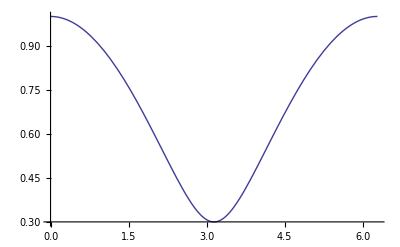

```mathematica
Plot[ej[0.3,ϕ] /.{ej0->1},{ϕ,0,2π},PlotRange->Full]
```

```mathematica
ϕs=Range[0,2.π,π/50.];
```

```mathematica
values=Join[{ϕs},Map[Block[{d=#},Map[ej[d,#] /.{ej0->1}&,ϕs]]&,Range[0,1,0.1]]]
```

{{0.,0.0628319,0.125664,0.188496,0.251327,0.314159,0.376991,0.439823,0.502655,0.565487,0.628319,0.69115,0.753982,0.816814,0.879646,0.942478,1.00531,1.06814,1.13097,1.19381,1.25664,1.31947,1.3823,1.44513,1.50796,1.5708,1.63363,1.69646,1.75929,1.82212,1.88496,1.94779,2.01062,2.07345,2.13628,2.19911,2.26195,2.32478,2.38761,2.45044,2.51327,2.57611,2.63894,2.70177,2.7646,2.82743,2.89027,2.9531,3.01593,3.07876,3.14159,3.20442,3.26726,3.33009,3.39292,3.45575,3.51858,3.58142,3.64425,3.70708,3.76991,3.83274,3.89557,3.95841,4.02124,4.08407,4.1469,4.20973,4.27257,4.3354,4.39823,4.46106,4.52389,4.58673,4.64956,4.71239,4.77522,4.83805,4.90088,4.96372,5.02655,5.08938,5.15221,5.21504,5.27788,5.34071,5.40354,5.46637,5.5292,5.59203,5.65487,5.7177,5.78053,5.84336,5.90619,5.96903,6.03186,6.09469,6.15752,6.22035,6.28319},{1.,0.999507,0.998027,0.995562,0.992115,0.987688,0.982287,0.975917,0.968583,0.960294,0.951057,0.940881,0.929776,0.917755,0.904827,0.891007,0.876307,0.860742,0.844328,0.827081,0.809017,0.790155,0.770513,0.750111,0.728969,0.707107,0.684547,0.661312,0.637424,0.612907,0.587785,0.562083,0.535827,0.509041,0.481754,0.45399,0.425779,0.397148,0.368125,0.338738,0.309017,0.278991,0.24869,0.218143,0.187381,0.156434,0.125333,0.0941083,0.0627905,0.0314108,0.,0.0314108,0.0627905,0.0941083,0.125333,0.156434,0.187381,0.218143,0.24869,0.278991,0.309017,0.338738,0.368125,0.397148,0.425779,0.45399,0.481754,0.509041,0.535827,0.562083,0.587785,0.612907,0.637424,0.661312,0.684547,0.707107,0.728969,0.750111,0.770513,0.790155,0.809017,0.827081,0.844328,0.860742,0.876307,0.891007,0.904827,0.917755,0.929776,0.940881,0.951057,0.960294,0.968583,0.975917,0.982287,0.987688,0.992115,0.995562,0.998027,0.999507,1.},{1.,0.999511,0.998046,0.995606,0.992194,0.987812,0.982466,0.976161,0.968902,0.960699,0.951558,0.94149,0.930505,0.918614,0.905828,0.892162,0.87763,0.862246,0.846026,0.828988,0.811149,0.792529,0.773145,0.753021,0.732176,0.710634,0.688418,0.665552,0.642064,0.617979,0.593327,0.568136,0.542438,0.516267,0.489659,0.462651,0.435287,0.407614,0.379685,0.351562,0.323321,0.295055,0.266886,0.238978,0.211567,0.185005,0.159848,0.136996,0.117912,0.10477,0.1,0.10477,0.117912,0.136996,0.159848,0.185005,0.211567,0.238978,0.266886,0.295055,0.323321,0.351562,0.379685,0.407614,0.435287,0.462651,0.489659,0.516267,0.542438,0.568136,0.593327,0.617979,0.642064,0.665552,0.688418,0.710634,0.732176,0.753021,0.773145,0.792529,0.811149,0.828988,0.846026,0.862246,0.87763,0.892162,0.905828,0.918614,0.930505,0.94149,0.951558,0.960699,0.968902,0.976161,0.982466,0.987812,0.992194,0.995606,0.998046,0.999511,1.},{1.,0.999526,0.998106,0.99574,0.992431,0.988184,0.983002,0.976891,0.969859,0.961913,0.953063,0.943317,0.932687,0.921185,0.908825,0.895621,0.881588,0.866742,0.851102,0.834685,0.817513,0.799607,0.780988,0.761682,0.741714,0.72111,0.6999,0.678115,0.655787,0.632952,0.609649,0.585918,0.561806,0.537362,0.512643,0.487712,0.462641,0.437513,0.412426,0.387497,0.362866,0.338707,0.315235,0.292717,0.271491,0.251978,0.234691,0.220232,0.209249,0.202354,0.2,0.202354,0.209249,0.220232,0.234691,0.251978,0.271491,0.292717,0.315235,0.338707,0.362866,0.387497,0.412426,0.437513,0.462641,0.487712,0.512643,0.537362,0.561806,0.585918,0.609649,0.632952,0.655787,0.678115,0.6999,0.72111,0.741714,0.761682,0.780988,0.799607,0.817513,0.834685,0.851102,0.866742,0.881588,0.895621,0.908825,0.921185,0.932687,0.943317,0.953063,0.961913,0.969859,0.976891,0.983002,0.988184,0.992431,0.99574,0.998106,0.999526,1.},{1.,0.999551,0.998204,0.995962,0.992827,0.988803,0.983894,0.978109,0.971452,0.963934,0.955564,0.946353,0.936312,0.925456,0.913799,0.901356,0.888145,0.874184,0.859494,0.844095,0.828011,0.811267,0.793888,0.775904,0.757344,0.738241,0.718631,0.698551,0.678042,0.65715,0.635922,0.614413,0.592681,0.570791,0.548816,0.526837,0.504948,0.483251,0.461865,0.440927,0.420592,0.401037,0.382466,0.365108,0.349216,0.335066,0.322947,0.313144,0.305921,0.301493,0.3,0.301493,0.305921,0.313144,0.322947,0.335066,0.349216,0.365108,0.382466,0.401037,0.420592,0.440927,0.461865,0.483251,0.504948,0.526837,0.548816,0.570791,0.592681,0.614413,0.635922,0.65715,0.678042,0.698551,0.718631,0.738241,0.757344,0.775904,0.793888,0.811267,0.828011,0.844095,0.859494,0.874184,0.888145,0.901356,0.913799,0.925456,0.936312,0.946353,0.955564,0.963934,0.971452,0.978109,0.983894,0.988803,0.992827,0.995962,0.998204,0.999551,1.},{1.,0.999586,0.998343,0.996273,0.993381,0.989668,0.985143,0.97981,0.973678,0.966756,0.959055,0.950587,0.941364,0.931402,0.920716,0.909324,0.897244,0.884498,0.871107,0.857095,0.842489,0.827315,0.811603,0.795387,0.778699,0.761577,0.744062,0.726196,0.708025,0.689602,0.670979,0.652218,0.633382,0.614543,0.595779,0.577174,0.558822,0.540824,0.523291,0.506344,0.490115,0.474744,0.460382,0.447183,0.435309,0.424919,0.416167,0.409194,0.404119,0.401035,0.4,0.401035,0.404119,0.409194,0.416167,0.424919,0.435309,0.447183,0.460382,0.474744,0.490115,0.506344,0.523291,0.540824,0.558822,0.577174,0.595779,0.614543,0.633382,0.652218,0.670979,0.689602,0.708025,0.726196,0.744062,0.761577,0.778699,0.795387,0.811603,0.827315,0.842489,0.857095,0.871107,0.884498,0.897244,0.909324,0.920716,0.931402,0.941364,0.950587,0.959055,0.966756,0.973678,0.97981,0.985143,0.989668,0.993381,0.996273,0.998343,0.999586,1.},{1.,0.99963,0.99852,0.996673,0.994092,0.990781,0.986745,0.981993,0.976532,0.970373,0.963525,0.956003,0.94782,0.938992,0.929534,0.919467,0.90881,0.897584,0.885814,0.873525,0.860745,0.847501,0.833827,0.819756,0.805324,0.790569,0.775534,0.760263,0.744803,0.729206,0.713525,0.69782,0.682153,0.66659,0.651203,0.636066,0.621262,0.606873,0.59299,0.579705,0.567114,0.555317,0.544413,0.5345,0.525675,0.518029,0.511646,0.506599,0.502948,0.500739,0.5,0.500739,0.502948,0.506599,0.511646,0.518029,0.525675,0.5345,0.544413,0.555317,0.567114,0.579705,0.59299,0.606873,0.621262,0.636066,0.651203,0.66659,0.682153,0.69782,0.713525,0.729206,0.744803,0.760263,0.775534,0.790569,0.805324,0.819756,0.833827,0.847501,0.860745,0.873525,0.885814,0.897584,0.90881,0.919467,0.929534,0.938992,0.94782,0.956003,0.963525,0.970373,0.976532,0.981993,0.986745,0.990781,0.994092,0.996673,0.99852,0.99963,1.},{1.,0.999684,0.998738,0.997162,0.994961,0.992138,0.9887,0.984655,0.980009,0.974774,0.968961,0.962582,0.955652,0.948185,0.9402,0.931714,0.922748,0.913324,0.903465,0.893196,0.882545,0.871539,0.86021,0.848591,0.836716,0.824621,0.812347,0.799933,0.787425,0.774867,0.762309,0.7498,0.737394,0.725147,0.713117,0.701362,0.689945,0.678929,0.668379,0.658358,0.648933,0.640168,0.632125,0.624864,0.618443,0.612913,0.60832,0.604705,0.602099,0.600526,0.6,0.600526,0.602099,0.604705,0.60832,0.612913,0.618443,0.624864,0.632125,0.640168,0.648933,0.658358,0.668379,0.678929,0.689945,0.701362,0.713117,0.725147,0.737394,0.7498,0.762309,0.774867,0.787425,0.799933,0.812347,0.824621,0.836716,0.848591,0.86021,0.871539,0.882545,0.893196,0.903465,0.913324,0.922748,0.931714,0.9402,0.948185,0.955652,0.962582,0.968961,0.974774,0.980009,0.984655,0.9887,0.992138,0.994961,0.997162,0.998738,0.999684,1.},{1.,0.999748,0.998994,0.997739,0.995986,0.99374,0.991006,0.987791,0.984103,0.979951,0.975346,0.970299,0.964825,0.958937,0.952651,0.945984,0.938955,0.931583,0.923891,0.915899,0.907634,0.89912,0.890383,0.881453,0.87236,0.863134,0.853808,0.844417,0.834996,0.825581,0.816211,0.806925,0.797763,0.788767,0.779977,0.771437,0.763189,0.755275,0.747739,0.740621,0.733962,0.727802,0.722179,0.717126,0.712676,0.708859,0.705699,0.703219,0.701435,0.700359,0.7,0.700359,0.701435,0.703219,0.705699,0.708859,0.712676,0.717126,0.722179,0.727802,0.733962,0.740621,0.747739,0.755275,0.763189,0.771437,0.779977,0.788767,0.797763,0.806925,0.816211,0.825581,0.834996,0.844417,0.853808,0.863134,0.87236,0.881453,0.890383,0.89912,0.907634,0.915899,0.923891,0.931583,0.938955,0.945984,0.952651,0.958937,0.964825,0.970299,0.975346,0.979951,0.984103,0.987791,0.991006,0.99374,0.995986,0.997739,0.998994,0.999748,1.},{1.,0.999822,0.99929,0.998405,0.997168,0.995585,0.99366,0.991397,0.988805,0.98589,0.982661,0.979128,0.975302,0.971194,0.966818,0.962186,0.957313,0.952216,0.946911,0.941415,0.935747,0.929927,0.923974,0.917911,0.911758,0.905539,0.899276,0.892995,0.886719,0.880475,0.874287,0.868181,0.862183,0.85632,0.850618,0.845103,0.8398,0.834734,0.829931,0.825414,0.821205,0.817326,0.813797,0.810636,0.807862,0.805487,0.803527,0.80199,0.800887,0.800222,0.8,0.800222,0.800887,0.80199,0.803527,0.805487,0.807862,0.810636,0.813797,0.817326,0.821205,0.825414,0.829931,0.834734,0.8398,0.845103,0.850618,0.85632,0.862183,0.868181,0.874287,0.880475,0.886719,0.892995,0.899276,0.905539,0.911758,0.917911,0.923974,0.929927,0.935747,0.941415,0.946911,0.952216,0.957313,0.962186,0.966818,0.971194,0.975302,0.979128,0.982661,0.98589,0.988805,0.991397,0.99366,0.995585,0.997168,0.998405,0.99929,0.999822,1.},{1.,0.999906,0.999625,0.999158,0.998507,0.997672,0.996659,0.995469,0.994107,0.992578,0.990887,0.989039,0.987042,0.984902,0.982627,0.980224,0.977703,0.975073,0.972342,0.969521,0.966621,0.963652,0.960625,0.957552,0.954445,0.951315,0.948175,0.945036,0.941912,0.938815,0.935758,0.932753,0.929812,0.926948,0.924173,0.921499,0.918937,0.916498,0.914193,0.912031,0.910024,0.908179,0.906505,0.905009,0.903699,0.902579,0.901657,0.900934,0.900416,0.900104,0.9,0.900104,0.900416,0.900934,0.901657,0.902579,0.903699,0.905009,0.906505,0.908179,0.910024,0.912031,0.914193,0.916498,0.918937,0.921499,0.924173,0.926948,0.929812,0.932753,0.935758,0.938815,0.941912,0.945036,0.948175,0.951315,0.954445,0.957552,0.960625,0.963652,0.966621,0.969521,0.972342,0.975073,0.977703,0.980224,0.982627,0.984902,0.987042,0.989039,0.990887,0.992578,0.994107,0.995469,0.996659,0.997672,0.998507,0.999158,0.999625,0.999906,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

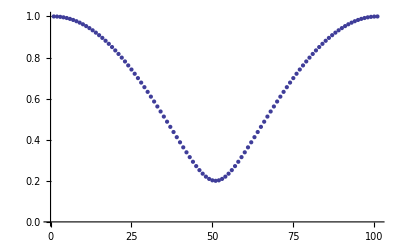

```mathematica
ListPlot[values[[4]]]
```

```mathematica
Export[NotebookDirectory[]<>"transmon_energy_vs_flux.csv",Transpose[values],"CSV"]
```

E:\cygwin\home\adewes\thesis\material\mathematica\transmon_energy_vs_flux.csv